```mathematica
SetDirectory["~/src/physics/FeynCalc/"]
$LoadFeynArts=True;
<<FeynCalc`
SetOptions[FourVector,FeynCalcInternal-> False]
FAPatch[PatchModelsOnly-> True]
```

/home/isanderson/src/physics/FeynCalc

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.11 (11 Apr 2019) patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

{Dimension→4,FeynCalcInternal→False}

Patching FeynArts models... done!

loading generic model file /home/isanderson/src/physics/FeynCalc/FeynArts/Models/SMDP_FA.gen

> $GenericMixing is OFF

generic model {SMDP_FA} initialized

loading classes model file /home/isanderson/src/physics/FeynCalc/FeynArts/Models/SMDP_FA.mod

> 46 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 74 vertices

classes model {SMDP_FA} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 0 Particles insertions

in total: 2 Particles insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

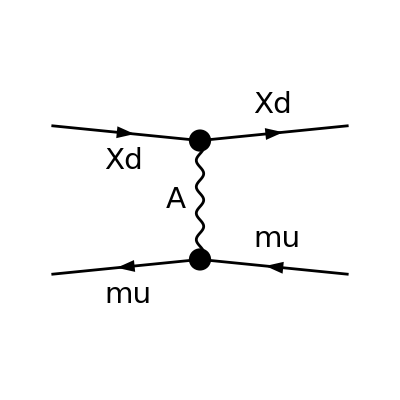

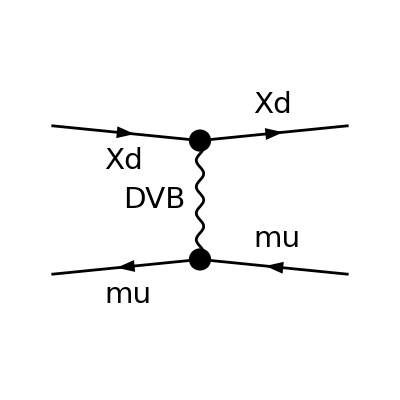

```mathematica
topElMuScat = CreateTopologies[0, 2 -> 2];
diagsElMuScat = InsertFields[topElMuScat, {F[13], -F[5]} ->
		{F[13], -F[5]}, InsertionLevel -> {Particles},
		Model -> "SMDP_FA",GenericModel-> "SMDP_FA"(*,ExcludeParticles-> {V[5],S[1],V[2]}*)];
Paint[diagsElMuScat, ColumnsXRows -> {1, 1}, Numbering -> None,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
ampElMuScat = FCFAConvert[CreateFeynAmp[diagsElMuScat, Truncated -> False],
IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,
ChangeDimension->4,List->False(*,SMP->True*)]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

-((ḡ)^Lor1Lor2 (φ(-OverBar[p2],MMU)).(ⅈ gc12 (γ̄)^Lor2).(φ(-OverBar[k2],MMU)) (φ(OverBar[k1],MXd)).(ⅈ gc7 (γ̄)^Lor1).(φ(OverBar[p1],MXd)))/((OverBar[k2]-OverBar[p2])^2-MDVB^2)-((ḡ)^Lor1Lor2 (φ(-OverBar[p2],MMU)).(ⅈ gc37 (γ̄)^Lor2).(φ(-OverBar[k2],MMU)) (φ(OverBar[k1],MXd)).(ⅈ gc6 (γ̄)^Lor1).(φ(OverBar[p1],MXd)))/(OverBar[k2]-OverBar[p2])^2

```mathematica
fengdσdER=8 π ϵ^2 αχ α Zn^2 mn/((u^2+vei[r]^2)(2mn ER +mA^2)^2)Exp[-ER/En];
SetMandelstam[s, t, u, p1, p2, -k1, -k2, MXd, MMU, MXd, MMU];
sqAmpElMuScat = (ampElMuScat (ComplexConjugate[ampElMuScat]//FCRenameDummyIndices))//
		PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/2^2]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//Simplify;
sqAmpElMuScat=sqAmpElMuScat/.M$FACouplings/.{FCGV("EL")-> ge}/.{MXd-> mχ,MDVB-> mA,MMU-> mn,gSM-> ϵ,ge-> √(4π α)Zn,gDM-> √(4π αχ)}
tp1={mχ+1/2 mχ v^2,mχ v,0};
tp2={mn,0,0};
tk1={mχ+1/2 mp3^2/mχ,mp3 cθ,-mp3 sθ};
tk2={mn + 1/2 mχ v^2-1/2 mp3^2/mχ,(mp1-cθ mp3),mp3 sθ};
v1=v/(1+m1/m2);
V1p={v1(Cos[θ] + m1/m2),v1 Sin[θ]}/.{θ-> π/2-θ/2,m1-> mχ,m2-> mn}//Simplify
mp3Rep=mχ √(V1p.V1p)//Simplify
srep=√({mχ + mn + 1/2 mχ v^2,mχ v}.{mχ + mn + 1/2 mχ v^2,mχ v});
trep=√{mχ + 1/2 mχ v^2+mχ + 1/2 mp3^2/mχ}
Reps={s->srep ,t->trep ,α-> 1/137.,αχ-> 0.035,mA-> 0.5,mχ-> 1000.,Zn-> 1,ϵ-> 10^-8,mn-> 0.9314941}
dσdΩ=(1/(8π))^2(mp3^2 sqAmpElMuScat)/(mn mp1 mp3 (E1+mn)-mp1 E3 Cos[θ])/.{mp1-> mχ v, mp3-> mp3Rep,E1-> mχ+1/2 mχ v^2,E3-> 1/2 mp3Rep/mχ}//.Reps//Simplify
2π NIntegrate[dσdΩ,{θ,0,π}]
```

(2 (2 mn^4+2 mn^2 (2 mχ^2-s+t-u)+2 mχ^4-2 mχ^2 (s-t+u)+s^2+u^2) (4 π √α √αχ Zn ϵ (t-mA^2)-4 π √α √αχ t Zn ϵ)^2)/(t^2 (mA^2-t)^2)

{(v (mn sin(θ/2)+mχ))/(mn+mχ),(mn v cos(θ/2))/(mn+mχ)}

mχ √((v^2 (mn^2+2 mn mχ sin(θ/2)+mχ^2))/(mn+mχ)^2)

√((mn+(mχ v^2)/2+mχ)^2+mχ^2 v^2)